# Grayscale Skeletonization

## Connectivity Functions, and Skeletonization

Initializations

```mathematica
Clear[rootPath];
rootPath = "C:\\_WashU\\ssa1\\source\\GrayscaleSkeleton\\";
```

```mathematica
Clear[gaussianRadius];
gaussianRadius = 4;
```

getProteinSlice
Gets a slice from the protein data set

```mathematica
Clear[getProteinSlice];
getProteinSlice[i_] := 
Module[{vol, maxVal,minVal},
vol := Get[rootPath <> "data\\proteinVolume.nb"];
maxVal = Max[Flatten[vol⟦i⟧]];
minVal = Min[Flatten[vol⟦i⟧]];
Return[Map[ Round[((#-minVal) *255.0)/(maxVal-minVal)]&, vol⟦i⟧, 1]];
];
```

getVolume
Gets a slice from the protein data set

```mathematica
Clear[getVolume];
getVolume[fileName_, xRange_, yRange_, zRange_] := 
Module[{vol, maxVal,minVal},
vol := Get[rootPath <> "data\\" <> fileName];
maxVal = Max[Flatten[vol]];
minVal = Min[Flatten[vol]];
Return[Take[Map[ Round[((#-minVal) *255.0)/(maxVal-minVal)]&, vol, 1], xRange, yRange, zRange]];
];
```

getImage
Gets a slice from a grayscale image

```mathematica
Clear[getImage];
getImage[imgName_] := Module[{picture},
picture=Import[rootPath <> "\\data\\" <> imgName];
Return[picture⟦1,1⟧];
];
```

getInput
Gets the input 
	1: Protein Sliced at 32
	2: Protein Sliced at 20
	3: Random.gif
	4: Blobs.gif
	5: Dragon.gif
	6: Letters.gif
	7: Rings.gif
	8: XWithGraySpots.gif
	9: Vessel
Also defines sliceSize which is a hash map of the pixels that span the image... The rest of the pixels make up a blank boundary which simplifies the calculations.

```mathematica
Clear[getInput];
getInput[i_] := 
Module[ {inputImage, sliceSize},
Switch[i,
1,inputImage = getImage["Protein32.gif"],
2, inputImage = getImage["Protein40.gif"],
3, inputImage = getImage["Random.gif"],
4, inputImage = getImage["Blobs.gif"],
5, inputImage = getImage["Dragon.gif"],
6, inputImage = getImage["Letters.gif"],
7, inputImage = getImage["Rings.gif"],
8, inputImage = getImage["XWithGraySpots.gif"],
9, inputImage = getImage["vessel_1.gif"],
10, inputImage = getImage["Basin.gif"],
11, inputImage = getImage["Basin2.gif"],
12, inputImage = getImage["BinaryText.gif"],
13, inputImage = getImage["BinaryMan.gif"],
14, inputImage = getImage["Question.gif"],
101, inputImage =  getImage["Protein32-surfaceRemoved.gif"],
102, inputImage = getImage["Protein40-surfaceRemoved.gif"],
103, inputImage = getImage["Random-surfaceRemoved.gif"],
104, inputImage = getImage["Blobs-surfaceRemoved.gif"],
105, inputImage = getImage["Dragon-surfaceRemoved.gif"],
106, inputImage = getImage["Letters-surfaceRemoved.gif"],
107, inputImage = getImage["Rings-surfaceRemoved.gif"],
108, inputImage = getImage["XWithGraySpots-surfaceRemoved.gif"],
109, inputImage = getImage["vessel_1-surfaceRemoved.gif"]
];

sliceSize[1,1] = 1;
sliceSize[2,1] = 1;
sliceSize[1,2] = Dimensions[inputImage]⟦1⟧;
sliceSize[2,2] = Dimensions[inputImage]⟦2⟧;
inputImage = Table[
If[(x >= sliceSize[1,1] )&&( x <= sliceSize[1,2] ) && (y >= sliceSize[2,1]) && (y <= sliceSize[2,2]),
inputImage⟦x,y⟧,
0
],
{x, 1-gaussianRadius, sliceSize[1,2]+gaussianRadius},
{y, 1-gaussianRadius, sliceSize[2,2]+gaussianRadius}
];
sliceSize[1,1] = gaussianRadius+1;
sliceSize[2,1] = gaussianRadius+1;
sliceSize[1,2] = Dimensions[inputImage]⟦1⟧-gaussianRadius;
sliceSize[2,2] = Dimensions[inputImage]⟦2⟧-gaussianRadius;
Return[{inputImage, sliceSize}];
];
```

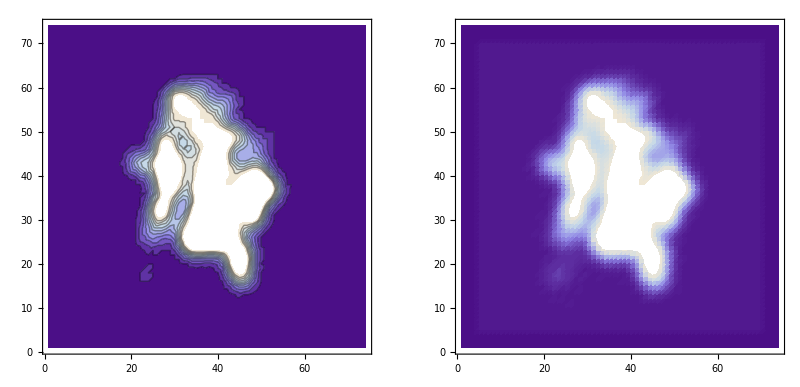

```mathematica
Clear[slice];
Clear[sliceSize];
inputs=getInput[1];
slice=inputs⟦1⟧;
sliceSize=inputs⟦2⟧;
Show[GraphicsRow[{ListContourPlot[slice,DisplayFunction->Identity,Contours->10],ListDensityPlot[slice,Mesh->False,DisplayFunction->Identity]}],DisplayFunction->$DisplayFunction]
Clear[inputs];
```

thresholdImage
Converts a grayscale image I into a binary image by setting all the values below the threshold t to zero

```mathematica
Clear[thresholdImage];
thresholdImage[I_, t_] := Map[If[# < t, 0, 1]&, I, {2}];
```

invertImage
Inverts an image

```mathematica
Clear[invertImage];
invertImage[I_] := Map[If[# == 0, 1, 0]&, I, {2}];
```

n4, n8
Returns the points in the 4 neighborhood and the 8 neighborhood of p

```mathematica
Clear[n4];
n4[p_] :={{p⟦1⟧, p⟦2⟧-1}, {p⟦1⟧, p⟦2⟧+1}, {p⟦1⟧-1, p⟦2⟧}, {p⟦1⟧+1, p⟦2⟧}};

Clear[n8];
n8[p_] :=Complement[Flatten[Table[{p⟦1⟧+x, p⟦2⟧+y},{ x, -1, 1 }, {y, -1, 1}], 1] , {p}];
```

getN4, getN8, getN4Immersion
Returns the points in the 4 / 8 neighborhood of p if it is in the thresholded image I

```mathematica
Clear[getN4];
getN4[p_, I_] := Select[n4[p], I⟦#⟦1⟧, #⟦2⟧⟧ > 0 &];
```

```mathematica
Clear[getN8];
getN8[p_, I_] := Select[n8[p], I⟦#⟦1⟧, #⟦2⟧⟧ > 0&];
```

```mathematica
Clear[getN4Immersion];
getN4Immersion[p_, V_] := getN4[{2,2},  thresholdImage[Take[V, {p⟦1⟧-1, p⟦1⟧+1}, {p⟦2⟧-1, p⟦2⟧+1}], V⟦p⟦1⟧, p⟦2⟧⟧]];
```

getC4
Gets the number of 4-connected elements around point p in the pointset X

```mathematica
Clear[getC4];
getC4[p_, testPoints_, imagePoints_] := 
Module [{tPoints, mImage, count, list, list2},
tPoints = testPoints;
mImage = imagePoints;
count = 0;
Scan[
If[MemberQ[tPoints, #], 
Module[{},
list = {#};
count = count + 1;
While[Length[list] > 0, 
Module[{},
list2 = {};
Scan[
Module[{},
tPoints = Complement[tPoints, {#}];
mImage = Complement[mImage, {#}];
list2 = Union[list2, Intersection[n4[#], mImage]];
] &, list];
list = list2;
]
]
]
] &,testPoints];
count
]
```

```mathematica
getC4[p_, X_] := getC4[p, X, X];
```

getC8
Gets the number of 8-connected elements around point p in the pointset X

```mathematica
Clear[getC8];
getC8[p_, testPoints_, imagePoints_] := 
Module [{tPoints, mImage, count, list, list2},
tPoints = testPoints;
mImage = imagePoints;
count = 0;
Scan[
If[MemberQ[tPoints, #], 
Module[{},
list = {#};
count = count + 1;
While[Length[list] > 0, 
Module[{},
list2 = {};
Scan[
Module[{},
tPoints = Complement[tPoints, {#}];
mImage = Complement[mImage, {#}];
list2 = Union[list2, Intersection[n8[#], mImage]];
] &, list];
list = list2;
]
]
]
] &,testPoints];
count
]
```

```mathematica
getC8[p_, X_] := getC8[p, X, X];
```

isCurveEnd
Tells us whether the point p is a curve end point in the image V

```mathematica
Clear[isCurveEnd];
isCurveEnd[p_, V_, W_] := 
Module[ {currentN4, n},
currentN4= getN4[p, V];
n = Length[currentN4];

Return[ (n==0) || ((n==1)&& isBoundaryPoint[currentN4⟦1⟧, V, W])];
]
```

isLocalMinima
Tells you whether the point p is a local minma in image V

```mathematica
Clear[isLocalMinima];
isLocalMinima[V_, p_] :=
Module[{currentN8, isAbove, isBelow},
currentN8 = n8[p];
isAbove = False;
isBelow = False;
Scan[
Module[{},
isAbove = isAbove || (V⟦#⟦1⟧, #⟦2⟧⟧ > V⟦p⟦1⟧, p⟦2⟧⟧);
isBelow = isBelow ||  (V⟦#⟦1⟧, #⟦2⟧⟧ < V⟦p⟦1⟧, p⟦2⟧⟧);
]&,  currentN8];
isAbove && !isBelow
]
```

isSimple
Tells us whether the point p is simple in the image V, inverse of the image W

```mathematica
Clear[isSimple];
isSimple[p_, V_, W_] :=((getC4[p, getN4[p, V], getN8[p, V]]  == 1) && (getC8[p, getN8[p, W], getN8[p, W]]  == 1));
```

isSimpleImmersion
Tells us whether the point p is simple in the image V,inverse of the image W when testing the immersion threshold

```mathematica
Clear[isSimpleImmersion];
isSimpleImmersion[p_, V_, threshold_] :=
Module[{V2, W2},
V2 = Take[V, {p⟦1⟧-1, p⟦1⟧+1}, {p⟦2⟧-1, p⟦2⟧+1}];
V2 = thresholdImage[V2, threshold];
W2 = invertImage[V2];
isSimple[{2,2}, V2, W2]
]
```

isBoundaryPoint
Tells us whether the point p is in the boundary point of the Image V, inverse of the image W

```mathematica
Clear[isBoundaryPoint];
isBoundaryPoint[p_, V_, W_] := ((V⟦p⟦1⟧, p⟦2⟧⟧ > 0) &&( Length[getN4[p, W]] > 0));
```

isBoundaryPointImmersion
Tells us whether the point p is in the boundary point of the Image V, inverse of the image W when performing immersion

```mathematica
Clear[isBoundaryPointImmersion];
isBoundaryPointImmersion[p_, V_] := (Length[Select[Map[{#⟦1⟧, #⟦2⟧, V⟦#⟦1⟧, #⟦2⟧⟧} &,  n4[p]], (#⟦3⟧ < V⟦p⟦1⟧, p⟦2⟧⟧) & ]] > 0);
```

isBorderingBackground
Tells us whether the point p is bordering a background pixel.

```mathematica
Clear[isBorderingBackground];
isBorderingBackground[p_, V_, W_] := ((V⟦p⟦1⟧, p⟦2⟧⟧ > 0) &&( Length[getN8[p, W]] > 0));
```

isDestructible
Tells us whether a point p can be destroyed from image V (inverse W) while preserving skeleton Pres..
	thinOperator = 0 → Topology preservation 
	thinOperator = 1 → Curve preservation 
	thinOperator = 2 → Surface preservation (To be implemented)

```mathematica
Clear[isDestructible];
isDestructible[p_, V_, W_, Pres_, thinOperator_] := 
If[thinOperator==0, 
(isBoundaryPoint[p, V, W] && isSimple[p, V, W] && (Pres⟦p⟦1⟧, p⟦2⟧⟧ == 0)), 
(isBoundaryPoint[p, V, W] && isSimple[p, V, W] && !isCurveEnd[p, V, W] && (Pres⟦p⟦1⟧, p⟦2⟧⟧ == 0))]
```

isSkeletalSurfacePoint
Lets us know whether a given skeletal point p is a surface point... 
	Pre: p is on the skeleton

```mathematica
Clear[isSkeletalSurfacePoint];
isSkeletalSurfacePoint[p_, S_] := 
Module[ {imageN8},
imageN8 = getN8[p, S];
Return[
((MemberQ[imageN8, {p⟦1⟧ , p⟦2⟧ + 1}] && MemberQ[imageN8, {p⟦1⟧ +1, p⟦2⟧ }] && MemberQ[imageN8, {p⟦1⟧+1 , p⟦2⟧ + 1}] ) ||(MemberQ[imageN8, {p⟦1⟧ , p⟦2⟧ - 1}] && MemberQ[imageN8, {p⟦1⟧ -1, p⟦2⟧ }] && MemberQ[imageN8, {p⟦1⟧-1 , p⟦2⟧ - 1}] ) ||
(MemberQ[imageN8, {p⟦1⟧ , p⟦2⟧ + 1}] && MemberQ[imageN8, {p⟦1⟧ -1, p⟦2⟧ }] && MemberQ[imageN8, {p⟦1⟧-1 , p⟦2⟧ + 1}] ) ||
(MemberQ[imageN8, {p⟦1⟧ , p⟦2⟧ - 1}] && MemberQ[imageN8, {p⟦1⟧ +1, p⟦2⟧ }] && MemberQ[imageN8, {p⟦1⟧+1 , p⟦2⟧ - 1}] ))
];
]
```

isSkeletalSurfaceInteriorPoint
Lets us know whether the point is an interior point of a surface

```mathematica
Clear[isSkeletalSurfaceInteriorPoint];
isSkeletalSurfaceInteriorPoint[p_, S_] :=(Length[getN8[p, S]] == 8);
```

getSkeletalPixelType
Gets the point type of a pixel p in the Skeleton S
	0 - Not in the skeleton
	1 - A skeletal point
	2 - A curve end point
	3 - A curve interior point
	4 - A surface boundary point
	5 - A surface interior point

```mathematica
Clear[getSkeletalPixelType];
getSkeletalPixelType[p_, S_] := 
Module[ {ret},
If[S⟦p⟦1⟧, p⟦2⟧⟧  ==0, 
ret = 0,
If[isSkeletalSurfacePoint[p, S],
If[isSkeletalSurfaceInteriorPoint[p, S], ret = 5, ret = 4],
If[Length[getN4[p, S]] == 0,
ret = 1,
If[Length[getN4[p, S]] == 1, ret = 2, ret = 3]
]
]
];
Return[ret];
]
```

getBlankImage
Returns a blank image of the same size as the source image.

```mathematica
Clear[getBlankImage] ;
getBlankImage[] := Table[0, {x, sliceSize[1,1]-gaussianRadius, sliceSize[1,2]+gaussianRadius}, {y, sliceSize[2,1]-gaussianRadius, sliceSize[2,2]+gaussianRadius}];
```

findSkeletalValue
Finds the correct skeletal value that a pixel can be reduced while performing immersion

```mathematica
Clear[findSkeletalValue];
findSkeletalValue[p_,V_]:=
Module[{neighbors,skelVal, V2, W2},
V2 = thresholdImage[Take[V, {p⟦1⟧-2,p⟦1⟧+2}, {p⟦2⟧-2,p⟦2⟧+2}], V⟦p⟦1⟧, p⟦2⟧⟧];
W2 = invertImage[V2];
If[isCurveEnd[{3,3}, V2, W2], 
V⟦p⟦1⟧, p⟦2⟧⟧,
Module[{},
neighbors=Sort[Map[{#⟦1⟧,#⟦2⟧,V⟦#⟦1⟧,#⟦2⟧⟧}&,Join[n4[p],{p}]],#1⟦3⟧>#2⟦3⟧&];
neighbors = Select[neighbors, #⟦3⟧ ≤ V⟦p⟦1⟧, p⟦2⟧⟧ &];
skelVal=neighbors⟦Length[neighbors],3⟧;
Do[
If[¬isSimpleImmersion[p,V,neighbors⟦i,3⟧],
Module[{},
skelVal=neighbors⟦i,3⟧;
Break[];
]];
,{i,1,Length[neighbors]}];
skelVal
]
]
];
```

performThinning
Performs the thinning operation on image V, (Inverse of the image W) for a maximum of n iterations, while preserving earlier skeleton Pres, for topology/curve or surface preservation.

```mathematica
Clear[performThinning];
performThinning[V_, W_, n_, Pres_, thinOperator_] :=
Module[{G,H,m, dMap, boundaryPoints, thicknessImage, thickness, progress},
m = Max[V];
G = V;
H = W;
thicknessImage = getBlankImage[];
thickness = 1;
progress = {};
Do[
(*progress = Join[progress, {ListDensityPlot[G, Mesh->False,Frame->False,  ColorFunctionScaling->True,  
ColorFunction->Function[{x}, GrayLevel[x]], ImageSize->{300,300}]}];*)
thickness = thickness+1;
dMap = Flatten[Table[If[isDestructible[{x, y}, G, H, Pres, thinOperator] , {x, y, Length[getN4[{x, y}, G]]}, {}], {x,sliceSize[1,1],sliceSize[1,2]}, {y,sliceSize[2,1], sliceSize[2,2]}], 1];
dMap = Select[dMap, Length[#]>0&];
dMap = Sort[dMap, (#2⟦3⟧>#1⟦3⟧)&];
If[Length[dMap] == 0, Break[]];

boundaryPoints = Flatten[Table[If[isBorderingBackground[{x,y}, G, H] , {x, y}, {}], {x,sliceSize[1,1],sliceSize[1,2]}, {y,sliceSize[2,1], sliceSize[2,2]}], 1];
boundaryPoints = Select[boundaryPoints, Length[#]>0&];
Scan[If[thicknessImage⟦#⟦1⟧, #⟦2⟧⟧ == 0,thicknessImage⟦#⟦1⟧, #⟦2⟧⟧= thickness]; &, boundaryPoints];
Scan[ If[isDestructible[{#⟦1⟧,#⟦2⟧}, G, H, Pres, thinOperator], Module[{},G⟦ #⟦1⟧,#⟦2⟧ ⟧  = 0;thicknessImage⟦ #⟦1⟧,#⟦2⟧ ⟧ = 0]];&,dMap];
H=invertImage[G];
, {i, n}];

boundaryPoints = Flatten[Table[If[isBorderingBackground[{x,y}, G, H] , {x, y}, {}], {x,sliceSize[1,1],sliceSize[1,2]}, {y,sliceSize[2,1], sliceSize[2,2]}], 1];
boundaryPoints = Select[boundaryPoints, Length[#]>0&];
Scan[If[thicknessImage⟦#⟦1⟧, #⟦2⟧⟧ == 0,thicknessImage⟦#⟦1⟧, #⟦2⟧⟧= thickness]; &, boundaryPoints];
(*progress = Join[progress, {ListDensityPlot[G, Mesh->False,Frame->False,  ColorFunctionScaling->True, ColorFunction->Function[{x}, GrayLevel[x]],  ImageSize->{300,300}]}];*)
Return[{G, thicknessImage, progress}];
]
```

performImmersionThinning
Performs shape perserving thinning on a grayscale volume

```mathematica
Clear[performImmersionThinning];
performImmersionThinning[V_, n_] :=
Module[{bins, V2, beach, modified, s0, s1, s2, s3, s4},
V2 = V;
Do[bins[i] = {},{i, 0, 255}];
Scan[bins[#⟦3⟧]=Join[bins[#⟦3⟧], {{#⟦1⟧, #⟦2⟧}}]; &,Flatten[Table[{x, y, V2⟦x,y⟧}, {x,1, Dimensions[V2]⟦1⟧}, {y,1, Dimensions[V2]⟦2⟧}], 1]];

Do[
s0 = Show[{ListDensityPlot[V2,Mesh->False, DisplayFunction->Identity], Graphics[{PointSize[0.001], RGBColor[0,0,1], Map[Point[#⟦{2,1}⟧ - {0.5, 0.5}] &, bins[g]]}]}];
Do[
modified = False;
beach = {};
Scan[If[isBoundaryPointImmersion[#, V2], beach = Join[beach, {{#⟦1⟧, #⟦2⟧, Length[getN4Immersion[#, V2]]}}]] &, bins[g]];
s1 = Show[{ListDensityPlot[V2,Mesh->False, DisplayFunction->Identity], Graphics[{PointSize[0.001],RGBColor[1,0,0], Map[Point[#⟦{2,1}⟧ - {0.5, 0.5}]  &, beach]}]}];
s4 = ListDensityPlot[Take[V2, {40,55}, {25,40}], Mesh->False, DisplayFunction->Identity];
If[Length[beach] == 0, Break[]];
(*beach = Sort[beach, #1⟦3⟧ < #2⟦3⟧ &];*)
Scan[
Module[{},
V2⟦#⟦1⟧, #⟦2⟧⟧ = findSkeletalValue[#, V2];
If[V2⟦#⟦1⟧, #⟦2⟧⟧ ≠ g,
Module[{},
bins[g] = Complement[bins[g], {#⟦{1,2}⟧}];
modified=True;
]
];
];&, beach];
s2 = Show[{ListDensityPlot[V2,Mesh->False, DisplayFunction->Identity],
 Graphics[{PointSize[0.001],RGBColor[1,0,0], Map[Point[#⟦{2,1}⟧ - {0.5, 0.5}]  &, Select[beach, V2⟦#⟦1⟧, #⟦2⟧⟧ == g &]]}],
 Graphics[{PointSize[0.001],RGBColor[0,0,1], Map[Point[#⟦{2,1}⟧ - {0.5, 0.5}]  &, Select[beach, V2⟦#⟦1⟧, #⟦2⟧⟧≠ g &]]}]}];
s3 = ListDensityPlot[Take[V2, {40,55}, {25,40}], Mesh->False, DisplayFunction->Identity];
(*If[g ≥ 99 && g ≤ 99, Show[GraphicsArray[{ s1, s2}], DisplayFunction->$DisplayFunction, ImageSize->{1600,800}, PlotLabel->ToString[g] <> " : " <> ToString[i]]];*)
If[¬modified, Break[]];
,{i, 1, n}];
,{g, 1, 255}];

V2
]
```

performErosion
Erodes the image by removing the curve end points

```mathematica
Clear[performErosion];
performErosion[V_, W_] := 
Module[
{dMap, outImage},
(*ListDensityPlot[V, Mesh->False, ImageSize->{600, 600}];*)
dMap = Flatten[Table[If[(isBoundaryPoint[{x, y}, V, W]  && isCurveEnd[{x, y}, V, W]) , {x, y}, {}], {x,sliceSize[1,1], sliceSize[1,2]}, {y,sliceSize[2,1], sliceSize[2,2]}], 1];
dMap = Select[dMap, Length[#]>0&];
outImage = V;
Scan[outImage⟦ #⟦1⟧,#⟦2⟧ ⟧  = 0;&,dMap];
(*ListDensityPlot[outImage, Mesh->False, ImageSize->{600, 600}]; *)
Return[outImage];
]
```

isCurveNeighbor
Specifies whether a given point q is a curve neighbor of the point p in image V

```mathematica
Clear[isCurveNeighbor];
isCurveNeighbor[q_, p_, V_] := 
Module[
{currentN4},
currentN4 = getN4[p, V];
Return[((Length[currentN4] == 2) && MemberQ[currentN4, q])];
]
```

addPixelToImage
Adds a pixel to a binary Image

```mathematica
Clear[addPixelToImage];
addPixelToImage[p_, V_] := 
Module[
{outImage},
outImage = V;
outImage⟦p⟦1⟧, p⟦2⟧⟧ =1;
Return[outImage];
]
```

getCurveNeighbors
Gets the curve neighbors of a given point p

```mathematica
Clear[getCurveNeighbors];
getCurveNeighbors[p_, V_] := 
Module[
{currentN4},
currentN4 = getN4[p, V];
Return[Select[currentN4, isCurveNeighbor[#, p, V]& ]];
]
```

performDilation
Dilates the image by adding curve end points

```mathematica
Clear[performDilation];
performDilation[V_, W_, oldV_] :=
Module[
{dMap, outImage, neighbors},
(*ListDensityPlot[V, Mesh->False, ImageSize->{600, 600}];*)
dMap = Flatten[Table[If[isBoundaryPoint[{x, y}, V, W]  && isCurveEnd[{x, y}, V, W] , {x, y}, {}], {x,sliceSize[1,1], sliceSize[1,2]}, {y,sliceSize[2,1], sliceSize[2,2]}], 1];
dMap = Select[dMap, Length[#]>0&];
neighbors = {};
Scan[neighbors = Join[neighbors, getCurveNeighbors[#, oldV]];&, dMap];
outImage = V;
Scan[outImage⟦#⟦1⟧, #⟦2⟧⟧ =1;&,neighbors];
(*ListDensityPlot[outImage, Mesh->False, ImageSize->{600, 600}]; *)
Return[outImage];
]
```

performPruning
Prunes the image n times.

```mathematica
Clear[performPruning];
performPruning[V_, W_, n_] :=
If[ n == 0, V, 
Module[
{erodedImage, prunedImage, dilatedImage},
(*ListDensityPlot[V, Mesh->False, ImageSize->{600, 600}];*)
erodedImage = performErosion[V, W];
prunedImage = performPruning[erodedImage, invertImage[erodedImage], n-1];
dilatedImage = performDilation[prunedImage, invertImage[prunedImage], V];
(*ListDensityPlot[dilatedImage, Mesh->False, ImageSize->{600, 600}]; *)
Return[dilatedImage];
]
]
```

getCurveLength:
Gets the length of a curve area given the starting point p, and the annotated skeleton A

```mathematica
Clear[getCurveLength];
getCurveLength[p_, A_, curveTypes_, hashKey_] :=
Module[ {n, dMap, dMap2, n4Temp, A2, toHash, doHash, curveEndPoints, allCurvePoints},
If[hashKey⟦2⟧ ≠ curveLengthHashKey⟦hashKey⟦1⟧⟧, 
Module[{}, 
curveLengthHashKey⟦hashKey⟦1⟧⟧ = hashKey⟦2⟧;
curveLengthHash⟦hashKey⟦1⟧⟧ = getBlankImage[];
]
];

If[curveLengthHash⟦hashKey⟦1⟧, p⟦1⟧, p⟦2⟧⟧ > 0, Return[curveLengthHash⟦hashKey⟦1⟧, p⟦1⟧, p⟦2⟧⟧]];

A2 = A;
dMap = Flatten[Table[If[!MemberQ[curveTypes, A⟦x,y⟧], {x, y}, {}], {x,sliceSize[1,1], sliceSize[1,2]}, {y,sliceSize[2,1], sliceSize[2,2]}], 1];
dMap = Select[dMap, Length[#]>0&];
Scan[A2⟦#⟦1⟧, #⟦2⟧⟧ = 0;&, dMap];

(*Show[{ListDensityPlot[A2, DisplayFunction->Identity],Graphics[{RGBColor[1,0,0],PointSize[0.02],Point[Reverse[p]+{-0.5,-0.5}]}]},DisplayFunction->$DisplayFunction];*)
n = 0;
toHash ={};
dMap = {p};
doHash = Length[getN4[p, A2]] ≤ 2;
curveEndPoints = {};
If[Length[getN4[p, A2]] ≠ 2, curveEndPoints = {p}];

allCurvePoints = {p};
While[ True,
toHash = Join[toHash, dMap];
dMap2 = {};
n = n + Length[dMap];
Scan[
Module[{},
A2⟦#⟦1⟧, #⟦2⟧⟧ = 0;
n4Temp= getN4[#, A2];
dMap2 = Join[dMap2,Select[n4Temp, (Length[getN4[#, A2]] ≤ 1)  &]]; 
allCurvePoints = Join[allCurvePoints,Select[n4Temp, (Length[getN4[#, A2]] ≤ 1)  &]]; 
curveEndPoints = Join[curveEndPoints,Select[n4Temp, (Length[getN4[#, A2]] ≠ 1)  &]]; 
];&, 
dMap];
dMap = dMap2;
If[Length[dMap] == 0, Break[]];
];

(*Show[{
ListDensityPlot[A, DisplayFunction->Identity],
Graphics[{RGBColor[1,0,0],PointSize[0.02],
Map[Point[Reverse[#]+{-0.5,-0.5}]&, allCurvePoints]}]},DisplayFunction->$DisplayFunction];*)

If[doHash, 
Scan[curveLengthHash⟦hashKey⟦1⟧, #⟦1⟧, #⟦2⟧⟧ = {n, curveEndPoints, allCurvePoints};&, toHash]];
Return[{n, curveEndPoints, allCurvePoints}];
]
```

getClosestValue:
Gets the closest value to a given pixel in the image

```mathematica
Clear[getClosestValue];
getClosestValue[p_, image_, level_] := 
Module[{n4List, closestValues},
If[image⟦p⟦1⟧, p⟦2⟧⟧ ≠ 0, Return[{{image⟦p⟦1⟧, p⟦2⟧⟧, level}}]];
If[level ≤ 0, Return[{{0, level}}]];

n4List = Select[n4[p], (#⟦1⟧ ≥ sliceSize[1,1])  && (#⟦1⟧ ≤ sliceSize[1,2]) && (#⟦2⟧ ≥ sliceSize[2,1])  && (#⟦2⟧ ≤ sliceSize[2,2])&];
closestValues = {};
Scan[closestValues = Join[closestValues, getClosestValue[#, image, level-1]];&, n4List];
closestValues = Sort[closestValues, (#1⟦2⟧ > #2⟦2⟧)&];
closestValues = Select[closestValues, #⟦2⟧ == closestValues⟦1,2⟧&];
closestValues = Sort[closestValues, (#1⟦1⟧ > #2⟦1⟧)&];
Return[{closestValues⟦1⟧}];
]
```

canRemovePixel:
Lets you know whether the given pixel can be removed from the skeleton based in the filter criteria.
Cost Function has the following values
	1: Remove if the length of the added segment >= filter threshold
	2: Remove if the length of the added segment / length of the total curve >= filter threshold
	3: Remove if the thickness difference between grayscale levels <= filter threshold
	4: Remove if the curve has not been growing recently
	5: Remove if the curve does not fall close to the eigen vector value

```mathematica
Clear[canRemovePixel];
canRemovePixel[p_, annotatedTopologyCurves_, annotatedCurves_, annotatedSkeleton_,thicknessMap_, curveEndHistory_, costFunction5Val_, currentGrayLevel_, filterThreshold_,  costFunction_, hashGrayValue_] :=
Module[{canRemove, type},
type = annotatedSkeleton⟦p⟦1⟧, p⟦2⟧⟧; 
canRemove = False;
Switch[costFunction,
1,Switch[type,
1, canRemove = False,
2, canRemove = getCurveLength[p, annotatedTopologyCurves, {2,3,4}, {1, hashGrayValue}]⟦1⟧ >= filterThreshold,
3, canRemove = getCurveLength[p, annotatedTopologyCurves, {2,3,4}, {1, hashGrayValue}]⟦1⟧ >= filterThreshold,
4, canRemove = getCurveLength[p, annotatedTopologyCurves, {2,3,4}, {1, hashGrayValue}]⟦1⟧ >= filterThreshold,
5, canRemove = True
],
2,Switch[type,
1, canRemove = False,
2, canRemove = (getCurveLength[p, annotatedTopologyCurves, {2,3,4}, {1, hashGrayValue}]⟦1⟧ / getCurveLength[p, annotatedSkeleton, {2,3,4}, {2, hashGrayValue}]⟦1⟧) >= filterThreshold,
3, canRemove = (getCurveLength[p, annotatedTopologyCurves, {2,3,4}, {1, hashGrayValue}]⟦1⟧/ getCurveLength[p, annotatedSkeleton, {2,3,4}, {2, hashGrayValue}]⟦1⟧) >= filterThreshold,
4, canRemove = (getCurveLength[p, annotatedTopologyCurves, {2,3,4}, {1, hashGrayValue}]⟦1⟧ / getCurveLength[p, annotatedSkeleton, {2,3,4}, {2, hashGrayValue}]⟦1⟧) >= filterThreshold,
5, canRemove = True
],
3, Module[{curveStats, curveLength, endPoints, thicknesses, totalThickness},
curveStats =  getCurveLength[p, annotatedSkeleton, {2,3,4}, {1, hashGrayValue}];
endPoints = curveStats⟦2⟧;
curveLength = curveStats⟦1⟧;
thicknesses = Map[thicknessMap⟦#⟦1⟧, #⟦2⟧⟧&, endPoints];
totalThickness = Sum[thicknesses⟦i⟧, {i, 1, Length[thicknesses]}];
Switch[type,
1, canRemove = False,
2, canRemove = (Length[thicknesses] == 2)&&(curveLength - totalThickness  ≤  filterThreshold),
3, canRemove =  (Length[thicknesses] == 2)&& (curveLength - totalThickness  ≤ filterThreshold),
4, canRemove =  (Length[thicknesses] == 2)&& (curveLength - totalThickness  ≤  filterThreshold),
5, canRemove = True
];
],
4, Module[{endPoints, endValues, endFailed},
endPoints =  getCurveLength[p, annotatedCurves, {2,3,4}, {1, hashGrayValue}]⟦2⟧;
endValues = Map[getClosestValue[#, curveEndHistory, 5]⟦1,1⟧&,endPoints];
endFailed = False;
Scan[endFailed = (endFailed || (# ≥ currentGrayLevel + filterThreshold));&,endValues];
Map
Switch[type,
1, canRemove = False, 
2, canRemove = endFailed,
3, canRemove =  endFailed,
4, canRemove =  endFailed,
5, canRemove = True
];
],
5, Module[
{},
Switch[type,
1, canRemove = False,
2, canRemove = True, (*costFunction5Val⟦p⟦1⟧, p⟦2⟧⟧ < filterThreshold,*)
3, canRemove = True, (*costFunction5Val⟦p⟦1⟧, p⟦2⟧⟧ < filterThreshold,*)
4, canRemove = True, (*costFunction5Val⟦p⟦1⟧, p⟦2⟧⟧ < filterThreshold,*)
5, canRemove = True
];
]
];
Return[canRemove];
];
```

annotateImageWithPixelType:
Annotates an image with the pixel type

```mathematica
Clear[annotateImageWithPixelType];
annotateImageWithPixelType[image_] := 
Module[{annotatedImage},
annotatedImage = getBlankImage[];
dMap = Flatten[Table[If[image⟦x, y⟧ > 0, {x, y, getSkeletalPixelType[{x,y}, image]}, {}], {x,sliceSize[1,1], sliceSize[1,2]}, {y,sliceSize[2,1], sliceSize[2,2]}], 1];
dMap = Select[dMap, Length[#]>0&];
Scan[annotatedImage⟦#⟦1⟧,#⟦2⟧⟧ = #⟦3⟧;&, dMap];
annotatedImage
];
```

makeGraySkeleton:
Creates a Gray scale skeleton of the grayImage, starting at the grayscale level startLevel, ending at endLevel at a grayscale step of step, while perfoming pruneAmount pruning steps.

```mathematica
Clear[makeGraySkeleton];
makeGraySkeleton[grayImage_,startLevel_,endLevel_,step_,pruneAmount_,filterThreshold_,costFunction_,eigenValues_]:=Module[{maxThinningIterations,olderSkeleton,graySkeleton,grayLevels,binaryImage,thinningResults,curveSkeleton,prunedCurveSkeleton,prunedCurveSkeletonWithOlder,topologySkeleton,topologyBranches,annotatedTopologyBranches,annotatedSkeleton,removedPixels,allRemovedPixels,dMap,thicknessMap,lastThicknessMap,actualGraySkeleton,allBranches,annotatedAllBranches,curveEndHistory,s1,s2,s3,s4,s5,s6,s7,s8,s9,s10,s11,s12},maxThinningIterations=100;olderSkeleton=getBlankImage[];graySkeleton=getBlankImage[];grayLevels=getBlankImage[];allRemovedPixels=getBlankImage[];curveEndHistory=getBlankImage[];lastThicknessMap=getBlankImage[];Do[binaryImage=thresholdImage[grayImage,i];thinningResults=performThinning[binaryImage,invertImage[binaryImage],maxThinningIterations,olderSkeleton,1];curveSkeleton=thinningResults⟦1⟧;prunedCurveSkeleton=performPruning[curveSkeleton,invertImage[curveSkeleton],pruneAmount];prunedCurveSkeletonWithOlder=BitOr[prunedCurveSkeleton,olderSkeleton];thinningResults=performThinning[binaryImage,invertImage[binaryImage],maxThinningIterations,prunedCurveSkeletonWithOlder,0];topologySkeleton=thinningResults⟦1⟧;thicknessMap=thinningResults⟦2⟧;topologyBranches=performThinning[topologySkeleton,invertImage[topologySkeleton],maxThinningIterations,olderSkeleton,0]⟦1⟧;topologyBranches=BitXor[olderSkeleton,topologyBranches];allBranches=BitXor[olderSkeleton,topologySkeleton];annotatedTopologyBranches=annotateImageWithPixelType[topologyBranches];annotatedSkeleton=annotateImageWithPixelType[topologySkeleton];annotatedAllBranches=annotateImageWithPixelType[allBranches];removedPixels=getBlankImage[];dMap=Flatten[Table[If[MemberQ[{1,2},annotatedSkeleton⟦x,y⟧]&&curveEndHistory⟦x,y⟧==0,{x,y},{}],{x,sliceSize[1,1],sliceSize[1,2]},{y,sliceSize[2,1],sliceSize[2,2]}],1];dMap=Select[dMap,Length[#1]>0&];Scan[(curveEndHistory⟦#1⟦1⟧,#1⟦2⟧⟧=i;)&,dMap];dMap=Flatten[Table[If[topologyBranches⟦x,y⟧==1&&canRemovePixel[{x,y},annotatedTopologyBranches,annotatedAllBranches,annotatedSkeleton,lastThicknessMap,curveEndHistory,eigenValues,i,filterThreshold,costFunction,i],{x,y},{}],{x,sliceSize[1,1],sliceSize[1,2]},{y,sliceSize[2,1],sliceSize[2,2]}],1];dMap=Select[dMap,Length[#1]>0&];Scan[(removedPixels⟦#1⟦1⟧,#1⟦2⟧⟧=1;)&,dMap];allRemovedPixels=BitOr[removedPixels,allRemovedPixels];dMap=Flatten[Table[If[topologySkeleton⟦x,y⟧==1&&graySkeleton⟦x,y⟧==0,{x,y},{}],{x,sliceSize[1,1],sliceSize[1,2]},{y,sliceSize[2,1],sliceSize[2,2]}],1];dMap=Select[dMap,Length[#1]>0&];Scan[(graySkeleton⟦#1⟦1⟧,#1⟦2⟧⟧=i;)&,dMap];olderSkeleton=topologySkeleton;lastThicknessMap=thicknessMap;actualGraySkeleton=graySkeleton;dMap=Flatten[Table[If[allRemovedPixels⟦x,y⟧==1,{x,y},{}],{x,sliceSize[1,1],sliceSize[1,2]},{y,sliceSize[2,1],sliceSize[2,2]}],1];dMap=Select[dMap,Length[#1]>0&];Scan[(actualGraySkeleton⟦#1⟦1⟧,#1⟦2⟧⟧=0;)&,dMap];s1=ListDensityPlot[binaryImage,Mesh->False,DisplayFunction->Identity,PlotLabel->"Binary Image"];s2=ListDensityPlot[curveSkeleton,Mesh->False,DisplayFunction->Identity,PlotLabel->"Curve Skeleton"];s3=ListDensityPlot[prunedCurveSkeleton,Mesh->False,DisplayFunction->Identity,PlotLabel->"Pruned Curve Skeleton"];s4=ListDensityPlot[prunedCurveSkeletonWithOlder,Mesh->False,DisplayFunction->Identity,PlotLabel->"Pruned Curve Skeleton with Older"];s5=ListDensityPlot[topologySkeleton,Mesh->False,DisplayFunction->Identity,PlotLabel->"Topology Skeleton"];s6=ListDensityPlot[graySkeleton,Mesh->False,DisplayFunction->Identity,PlotLabel->"Grayscale Skeleton"];s7=ListDensityPlot[topologyBranches,Mesh->False,DisplayFunction->Identity,PlotLabel->"Topology Branches"];s8=ListDensityPlot[removedPixels,Mesh->False,DisplayFunction->Identity,PlotLabel->"Removed Pixels"];s9=ListDensityPlot[allRemovedPixels,Mesh->False,DisplayFunction->Identity,PlotLabel->"All Removed Pixels"];s10=ListDensityPlot[actualGraySkeleton,Mesh->False,DisplayFunction->Identity,PlotLabel->"Actual Grayskeleton"];s11=ListDensityPlot[curveEndHistory,Mesh->False,DisplayFunction->Identity,PlotLabel->"Curve End History"];s12=ListDensityPlot[allBranches,Mesh->False,DisplayFunction->Identity,PlotLabel->"All Branches"];s13=ListDensityPlot[annotatedSkeleton,Mesh->False,DisplayFunction->Identity,PlotLabel->"Annotated Skeleton"];Show[GraphicsRow[{s1,s4,s5,s6,s12,s9,s10}],PlotLabel->"Grayscale value: "<>ToString[i],DisplayFunction->$DisplayFunction,ImageSize->{1200,1200/5}],{i,endLevel,startLevel,-step}];Return[{graySkeleton,actualGraySkeleton}];]
```

cleanImmersionSkeleton
Performs a post-processing step on the grayscale skeleton to prune it using the pruning parameter, and to remove surfaces.

```mathematica
Clear[cleanImmersionSkeleton];
cleanImmersionSkeleton[skel_, pruneAmount_] := 
Module[{bins, binarySkel, newSkel},
newSkel = skel;
Do[bins[i] = {},{i, 0, 255}];
Scan[bins[#⟦3⟧]=Join[bins[#⟦3⟧], {{#⟦1⟧, #⟦2⟧}}]; &,Flatten[Table[{x, y, skel⟦x, y⟧}, {x,1, Dimensions[skel]⟦1⟧}, {y,1, Dimensions[skel]⟦2⟧}], 1]];
Do[
binarySkel = thresholdImage[skel, g];
Scan[If[isSkeletalSurfaceInteriorPoint[#⟦{1,2}⟧, binarySkel], newSkel⟦#⟦1⟧, #⟦2⟧⟧ = 0]; &,bins[g]];
,{g, 255, 1, -1}];
newSkel
]
```

## Structure Tensor Methods

getGradientField:
Gets the gradient field of the image

```mathematica
Clear[getGradientField];
getGradientField[arr_]:=
Module[
{grad,len,wid},
grad = Map[Map[{0,0}&,#]&,arr];
{len,wid}=Dimensions[arr];
Do[
grad⟦x,y⟧={arr⟦x+1,y⟧-arr⟦x-1,y⟧,arr⟦x,y+1⟧-arr⟦x,y-1⟧},
{x,2,len-1},{y,2,wid-1}];
grad
];
```

getGradientField3D:
Gets the gradient field of the image

```mathematica
Clear[getGradientField3D];
getGradientField3D[arr_]:=
Module[
{grad,len,wid},
grad = Map[Map[Map[{0,0,0}&,#]&,#]&,arr];
{len,wid, hei}=Dimensions[arr];
Do[
grad⟦x,y, z⟧={arr⟦x+1,y, z⟧-arr⟦x-1,y, z⟧,arr⟦x,y+1, z⟧-arr⟦x,y-1, z⟧,arr⟦x,y, z+1⟧-arr⟦x,y, z-1⟧},
{x,2,len-1},{y,2,wid-1}, {z, 2, hei-1}];
grad
];
```

getGaussianMask:
Gets a Gaussian Mask

```mathematica
Clear[getGaussianMask];
getGaussianMask[a_]:=
Module[
{res},
res = Flatten[Table[Binomial[2*a,Floor[√(x^2+y^2)]+a],{x,-a,a},{y,-a,a}]];
N[res/Tr[res]]
];
```

getGaussianMask3D:
Gets a Gaussian Mask

```mathematica
Clear[getGaussianMask3D];
getGaussianMask3D[a_]:=
Module[
{res},
res = Flatten[Table[Binomial[2*a,Floor[√(x^2+y^2+z^2)]+a],{x,-a,a},{y,-a,a}, {z, -a, a}]];
N[res/Tr[res]]
];
```

getLocalStructureTensor:
Gets the local structure tensor given the gradient field grad_ and the mask width a_

```mathematica
Clear[getLocalStructureTensor];
getLocalStructureTensor[grad_,a_]:=
Module[
{tensors,lst, len,wid,t,mask},
tensors=Map[Map[(Transpose[{#}].{#})&,#]&,grad];
lst=Map[Map[{{0,0},{0,0}}&,#]&,grad];
len=Length[grad];
wid=Length[grad⟦1⟧];
mask=getGaussianMask[a];
Do[
lst⟦x,y⟧=mask.Flatten[Take[tensors,{x-a,x+a},{y-a,y+a}],1];,
{x,a+1,len-a},{y,a+1,wid-a}];
lst];
```

getLocalStructureTensor:
Gets the local structure tensor given the gradient field grad_ and the mask width a_

```mathematica
Clear[getLocalStructureTensor3D];
getLocalStructureTensor3D[grad_,a_, mask_, skel_]:=
Module[
{tensors,lst, len,wid,t, temp},
tensors=Map[Map[Map[(Transpose[{#}].{#})&,#]&, #]&,grad];
lst=Map[Map[Map[{{0,0,0},{0,0,0}, {0,0,0}}&,#]&, #]&,grad];
{len, wid, hei, temp}=Dimensions[grad];
Do[
If[skel⟦x, y, z⟧ > 0, 
lst⟦x,y, z⟧=mask.Flatten[Take[tensors,{x-a,x+a},{y-a,y+a}, {z-a, z+a}],2];],
{x,a+1,len-a},{y,a+1,wid-a}, {z,a+1,hei-a}];
lst
];
```

normalizeVector:
Normalizes a vector

```mathematica
Clear[normalizeVector];
normalizeVector[v_]:=
If[v.v ≠ 0, v/√(v.v), {0,0}];
```

normalizeVector3D:
Normalizes a vector

```mathematica
Clear[normalizeVector3D];
normalizeVector3D[v_]:=
If[v.v ≠ 0, v/√(v.v), {0,0,0}];
```

getEigen:
Gets the eigen values of a list of structure tensors

```mathematica
Clear[getEigen];
getEigen[lst_]:=Map[Map[Eigensystem,#]&,lst];
```

getEigen3D:
Gets the eigen values of a list of structure tensors

```mathematica
Clear[getEigen3D];
getEigen3D[lst_, skel_]:=
Module[{eigs},
eigs=Map[Map[Map[{{0,0,0}, {{0,0,0},{0,0,0},{0,0,0}}}&,#]&, #]&,grad];
Do[
If[skel⟦x, y, z⟧ > 0, 
eigs⟦x,y,z⟧=Eigensystem[lst⟦x,y,z⟧];],
{x,1,len},{y,1,wid}, {z,1,hei}];
eigs
]
```

lst=getLocalStructureTensor[getGradientField[slice],gaussianRadius];
eigens=getEigen[lst];
Show[{ListDensityPlot[slice/255.0,Mesh→False,ColorFunctionScaling→False,DisplayFunction→Identity],Graphics[{RGBColor[0,0,1],Table[If[eigens⟦x,y,1,1⟧>0,Line[{{y,x},{y,x}+Reverse[normalizeVector[eigens⟦x,y,2,2⟧]]*(1-eigens⟦x,y,1,2⟧/eigens⟦x,y,1,1⟧)}],Circle[{y,x},0.01]],{x,Length[eigens]},{y,Length[eigens⟦1⟧]}]},AspectRatio→Automatic,PlotRange→{{0,65},{0,65}},Frame→True,DisplayFunction→Identity]},DisplayFunction→$DisplayFunction];

getCostFunction5:
Returns the cost of adding in a new pixel based on the structure tensor eigen analysis.

```mathematica
Clear[getCostFunction5];
getCostFunction5[p_,  eigenValues_,  skeletonDirections_, annotatedSkeleton_] := 
Module[{cost},
cost = 0;
If[(eigenValues⟦p⟦1⟧, p⟦2⟧, 1, 1⟧ ≠ 0),
cost = 1 -(Abs[skeletonDirections⟦p⟦1⟧, p⟦2⟧⟧ . eigenValues⟦p⟦1⟧, p⟦2⟧, 2, 1⟧]) * (1- Abs[eigenValues⟦p⟦1⟧, p⟦2⟧, 1, 2⟧ /  eigenValues⟦p⟦1⟧, p⟦2⟧, 1, 1⟧] )];

If[annotatedSkeleton⟦p⟦1⟧, p⟦2⟧⟧ == 1, 
cost = Abs[eigenValues⟦p⟦1⟧, p⟦2⟧, 1, 2⟧ /  eigenValues⟦p⟦1⟧, p⟦2⟧, 1, 1⟧] ];
Return[cost];
];
```

getCostFunction5Image:
Gets an image annotated using the 5th cost function (Eigen Analysis)

```mathematica
Clear[getCostFunction5Image];
getCostFunction5Image[skeleton_, eigenValues_, skeletonDirections_, annotatedSkeleton_] :=
Module[{retVal, s2},
s2 = skeleton;
retVal = Table[
If[s2⟦x, y⟧ > 0, 
getCostFunction5[{x,y},  eigenValues,  skeletonDirections, annotatedSkeleton],
0],
{x, 1, Dimensions[skeleton]⟦1⟧}, 
{y, 1, Dimensions[skeleton]⟦2⟧}];
Return[retVal];
];
```

getSkeletonDirection:
Gets the Vector field of the skeleton

```mathematica
Clear[getSkeletonDirection];
getSkeletonDirection[skeleton_] := 
Module[{direction, defaultDirections},
defaultDirections = getEigen[getLocalStructureTensor[getGradientField[skeleton],1]];
direction = Table[
If[skeleton⟦x,y⟧ > 0, 
Module[{n4, dir},
n4 = getN4[{x,y}, skeleton];
dir = defaultDirections⟦x,y,2,2⟧;
Switch[Length[n4],
1, dir = n4⟦1⟧ - {x,y};,
2, dir = n4⟦2⟧ - n4⟦1⟧];
normalizeVector[dir]
], 
{0,0}],
 {x, 1, Dimensions[skeleton]⟦1⟧}, 
{y, 1, Dimensions[skeleton]⟦2⟧}
];
Return[direction]
];
```

doSkeletonCleanup:
Cleans up the skeleton using cost function 5

```mathematica
Clear[doSkeletonCleanup];
doSkeletonCleanup[sourceImage_,skeleton_,threshold_,stepSize_,showGeneralPlots_,showIterationPlots_]:=Module[{sourceEigens,binarySkeleton,skeletonDirections,pixelCosts,prunedSkeleton,newPixels,annotatedNewPixels,grayValueSkeleton,p1,p2,p3,p4,p5,p6,p7,p01,p02,p03},sourceEigens=getEigen[getLocalStructureTensor[getGradientField[sourceImage],gaussianRadius]];binarySkeleton=thresholdImage[skeleton,1];skeletonDirections=getSkeletonDirection[binarySkeleton];pixelCosts=getCostFunction5Image[binarySkeleton,sourceEigens,skeletonDirections,annotateImageWithPixelType[binarySkeleton]];prunedSkeleton=getBlankImage[];If[showGeneralPlots,Module[{},p1=ListDensityPlot[sourceImage,Mesh->False,DisplayFunction->Identity,PlotLabel->"Source Image"];p2=ListDensityPlot[skeleton,Mesh->False,DisplayFunction->Identity,PlotLabel->"Grayscale Skeleton"];p3=ListDensityPlot[binarySkeleton,Mesh->False,DisplayFunction->Identity,PlotLabel->"Binary Skeleton"];p4=Show[{ListDensityPlot[sourceImage/255.,Mesh->False,ColorFunctionScaling->False,DisplayFunction->Identity],Graphics[{RGBColor[0,0,1],Table[If[sourceEigens⟦x,y,1,1⟧>0,Line[{{y-0.5,x-0.5},{y-0.5,x-0.5}+Reverse[normalizeVector[sourceEigens⟦x,y,2,2⟧]] (1-sourceEigens⟦x,y,1,2⟧/sourceEigens⟦x,y,1,1⟧)}],Line[{{y-0.5,x-0.5},{y-0.5,x-0.5}}]],{x,Length[sourceEigens]},{y,Length[sourceEigens⟦1⟧]}]},AspectRatio->Automatic,PlotRange->{{0,65},{0,65}},Frame->True,DisplayFunction->Identity]},DisplayFunction->Identity,PlotLabel->"Source Vector Field"];p5=Show[{ListDensityPlot[thresholdImage[skeleton,1]/255.,Mesh->False,ColorFunctionScaling->False,DisplayFunction->Identity],Graphics[{RGBColor[0,0,1],Table[Line[{{y-0.5,x-0.5},{y-0.5,x-0.5}+Reverse[1/2 normalizeVector[skeletonDirections⟦x,y⟧]]}],{x,Length[skeletonDirections]},{y,Length[skeletonDirections⟦1⟧]}]},AspectRatio->Automatic,PlotRange->{{0,65},{0,65}},Frame->True,DisplayFunction->Identity]},DisplayFunction->Identity,PlotLabel->"Skeleton Vector Field"];p6=Show[{ListDensityPlot[slice/255.,Mesh->False,ColorFunctionScaling->False,DisplayFunction->Identity],Graphics[{RGBColor[0,0,1],Table[If[sourceEigens⟦x,y,1,1⟧>0,Line[{{y-0.5,x-0.5},{y-0.5,x-0.5}+Reverse[normalizeVector[sourceEigens⟦x,y,2,2⟧]] (1-sourceEigens⟦x,y,1,2⟧/sourceEigens⟦x,y,1,1⟧)}],Line[{{y-0.5,x-0.5},{y-0.5,x-0.5}}]],{x,Length[sourceEigens]},{y,Length[sourceEigens⟦1⟧]}]},AspectRatio->Automatic,PlotRange->{{0,65},{0,65}},Frame->True,DisplayFunction->Identity],Graphics[{RGBColor[1,0,0],Table[Line[{{y-0.5,x-0.5},{y-0.5,x-0.5}+Reverse[1/2 normalizeVector[skeletonDirections⟦x,y⟧]]}],{x,Length[skeletonDirections]},{y,Length[skeletonDirections⟦1⟧]}]},AspectRatio->Automatic,PlotRange->{{0,65},{0,65}},Frame->True,DisplayFunction->Identity]},DisplayFunction->Identity,PlotLabel->"Source  Field on Skeleton Field"];p7=ListDensityPlot[pixelCosts,Mesh->False,DisplayFunction->Identity,PlotLabel->"Cost Function"];Show[GraphicsGrid[{{p1,p2,p3},{p4,p5,p6},{p7}}],ImageSize->{1200,1200}]];];Do[grayValueSkeleton=thresholdImage[skeleton,grayValue];newPixels=grayValueSkeleton-prunedSkeleton;annotatedNewPixels=annotateImageWithPixelType[newPixels];skeletonDirections=getSkeletonDirection[grayValueSkeleton];pixelCosts=getCostFunction5Image[grayValueSkeleton,sourceEigens,skeletonDirections,annotatedNewPixels];If[showIterationPlots,p01=ListDensityPlot[newPixels,Mesh->False,DisplayFunction->Identity,PlotLabel->"New Pixels"];];dMap=Flatten[Table[If[newPixels⟦x,y⟧>0,{x,y},{}],{x,sliceSize[1,1],sliceSize[1,2]},{y,sliceSize[2,1],sliceSize[2,2]}],1];dMap=Select[dMap,Length[#1]>0&];Scan[(If[newPixels⟦#1⟦1⟧,#1⟦2⟧⟧>0,Module[{curvePoints,curveCost},curvePoints=getCurveLength[#1,annotatedNewPixels,{1,2,3,4},{1,grayValue}]⟦3⟧;curveCost=(∑_(i=1)^Length[curvePoints] ((pixelCosts⟦#1⟦1⟧,#1⟦2⟧⟧&)/@curvePoints)⟦i⟧)/Length[curvePoints];If[curveCost≥threshold,Scan[(prunedSkeleton⟦#1⟦1⟧,#1⟦2⟧⟧=1;)&,curvePoints];];Scan[(newPixels⟦#1⟦1⟧,#1⟦2⟧⟧=0;)&,curvePoints];];];)&,dMap];If[showIterationPlots,p02=ListDensityPlot[prunedSkeleton,Mesh->False,DisplayFunction->Identity,PlotLabel->"Pruned Skeleton"];p03=Show[{ListDensityPlot[slice/255.,Mesh->False,ColorFunctionScaling->False,DisplayFunction->Identity],Graphics[{RGBColor[0,0,1],Table[If[sourceEigens⟦x,y,1,1⟧>0,Line[{{y-0.5,x-0.5},{y-0.5,x-0.5}+Reverse[normalizeVector[sourceEigens⟦x,y,2,2⟧]] (1-sourceEigens⟦x,y,1,2⟧/sourceEigens⟦x,y,1,1⟧)}],Line[{{y-0.5,x-0.5},{y-0.5,x-0.5}}]],{x,Length[sourceEigens]},{y,Length[sourceEigens⟦1⟧]}]},AspectRatio->Automatic,PlotRange->{{0,65},{0,65}},Frame->True,DisplayFunction->Identity],Graphics[{RGBColor[1,0,0],Table[Line[{{y-0.5,x-0.5},{y-0.5,x-0.5}+Reverse[1/2 normalizeVector[skeletonDirections⟦x,y⟧]]}],{x,Length[skeletonDirections]},{y,Length[skeletonDirections⟦1⟧]}]},AspectRatio->Automatic,PlotRange->{{0,65},{0,65}},Frame->True,DisplayFunction->Identity]},DisplayFunction->Identity,PlotLabel->"Source  Field on Skeleton Field"];p04=ListDensityPlot[pixelCosts,Mesh->False,DisplayFunction->Identity,PlotLabel->"Cost Function"];Show[GraphicsRow[{p01,p02,p03,p04}],ImageSize->{1200,300},PlotLabel->"Gray Value : "<>ToString[grayValue]]];,{grayValue,255,1,stepSize}];newSkeleton=skeleton;dMap=Flatten[Table[If[prunedSkeleton⟦x,y⟧==0,{x,y},{}],{x,sliceSize[1,1],sliceSize[1,2]},{y,sliceSize[2,1],sliceSize[2,2]}],1];dMap=Select[dMap,Length[#1]>0&];Scan[(newSkeleton⟦#1⟦1⟧,#1⟦2⟧⟧=0;)&,dMap];{newSkeleton,prunedSkeleton}]
```

## Statistical Profiles

getPriorVal
Gets the earlier value in the histogram table

```mathematica
Clear[getPriorVal];
getPriorVal[hist_, currentIndex_] :=
Module[{priorVal, cVal, pVal, i},
priorVal = 0;
cVal = hist⟦currentIndex, 2⟧;
i = currentIndex - 1;
While[i >= 1,
priorVal = hist⟦i, 2⟧;
Break[];
i--;
];
priorVal
]
```

getNextVal
Gets the next value in the histogram table

```mathematica
Clear[getNextVal];
getNextVal[hist_, currentIndex_] :=
Module[{nextVal, cVal, nVal, i},
nextVal = 0;
cVal = hist⟦currentIndex, 2⟧;
i = currentIndex + 1;
While[i <= Length[hist],
nVal = hist⟦i, 2⟧;
If[nVal ≠ cVal, Module[{}, nextVal = nVal; Break[]]];
i++;
];
nextVal
]
```

smudgeHistogram
Smudges a histogram by averaging the neighbors

```mathematica
Clear[smudgeHistogram];
smudgeHistogram[hist_] :=
Module[{newHist},
newHist = Table[0, {Length[hist]-1}, {2}];
Do[
newHist⟦i,1⟧ = ( hist⟦i,1⟧ + hist⟦i+1,1⟧) / 3.0;
newHist⟦i,2⟧ = (hist⟦i,2⟧ + hist⟦i+1,2⟧) / 3.0;
,{i, 1, Length[hist]-1}
];
newHist
]
```

getPeakCount
Counts the number of peaks

```mathematica
Clear[getPeakCount];
getPeakCount[hist_,s_]:=
Module[{priorVal,currVal,nextVal,n, newHist},
newHist = hist;
Do[newHist = smudgeHistogram[newHist], {s}];
n=0;
Do[
priorVal=getPriorVal[newHist, i];
currVal=newHist⟦i,2⟧;
nextVal=getNextVal[newHist, i];
If[(currVal > priorVal )&& ( currVal > nextVal), n++];
,{i,1,Length[newHist]}];
n
]
```

getTypeDurationGraph
Displays a graph of how long a skeletal point stays as a skeletal type

```mathematica
Clear[getTypeDurationGraph];
getTypeDurationGraph[stats_, types_] :=
Module[
{image, newStats},
image = getBlankImage[];
newStats = Select[stats, MemberQ[types, #⟦1⟧]&];
Scan[image⟦ #⟦2⟧, #⟦3⟧⟧++;&,newStats];
ListDensityPlot[Map[#&, image, 1], Mesh->True, ColorFunctionScaling->True,DisplayFunction->Identity ]
]
```

getTypeLengthSummationGraph
Displays a graph of the cumulative length / area of a curve or surface

```mathematica
Clear[getTypeLengthSummationGraph];
getTypeLengthSummationGraph[stats_, types_] :=
Module[
{image, newStats},
image = getBlankImage[];
newStats = Select[stats, MemberQ[types, #⟦1⟧]&];
Scan[image⟦ #⟦2⟧, #⟦3⟧⟧ +=  #⟦6⟧;&,newStats];
ListDensityPlot[Map[#&, image, 1], Mesh->False, ColorFunctionScaling->True, DisplayFunction->Identity]
]
```

getThicknessHistogram
Gets the list of thicknesses and their frequencies

```mathematica
Clear[getThicknessHistogram];
getThicknessHistogram[list_]:=Module[{tList,plot},tList=Table[{-1,0},{x,0,sliceSize[1,2] sliceSize[2,2]}];Scan[(tList⟦#1⟦2⟧+1⟧={#1⟦2⟧,tList⟦#1⟦2⟧+1⟧⟦2⟧+1};)&,list];tList=Select[tList,#1⟦1⟧≠-1&];If[Length[tList]>0,plot=ListPlot[tList,Joined->True,PlotRange->All,DisplayFunction->Identity]];{tList,plot}]
```

getPeakCountForImage
Gets a plot of the number of histogram peaks there are at each point

```mathematica
Clear[getPeakCountForImage];
getPeakCountForImage[stats_, types_, skel_, noiseValue_]:=
Module[{newStats, img},
newStats = Select[stats, MemberQ[types, #⟦1⟧]&];
img = getBlankImage[];
Do[
Do[
If[skel⟦x,y⟧ > 0, 
Module[{thicknessData},
thicknessData = getThicknessListAndGraph[{x,y}, stats, types];
img⟦x,y⟧ = getPeakCount[thicknessData⟦2,1⟧ ,noiseValue];
]
];
,{y,sliceSize[2,1], sliceSize[2,2]}];
,{x, sliceSize[1,1], sliceSize[1,2]}];
img
]
```

getThicknessListAndGraph
Gets the list of thickness information and the graph of how the thickness changes along the grayscale value

```mathematica
Clear[getThicknessListAndGraph];
getThicknessListAndGraph[p_,stats_,types_]:=Module[{d,newStats,plot},newStats=Select[stats,MemberQ[types,#1⟦1⟧]&];d=Select[newStats,#1⟦2⟧==p⟦1⟧&&#1⟦3⟧==p⟦2⟧&];d=Sort[d,#1⟦4⟧<#2⟦4⟧&];d=(#1⟦{4,5}⟧&)/@d;If[Length[d]>0,plot=ListPlot[d,Joined->True,PlotRange->All,DisplayFunction->Identity,AxesLabel->{"Grayscale","Thickness"}]];{{d,{plot}},getThicknessHistogram[d]}];
```

displayThicknessStatisticsPerPoint
Displays the thickness statistics graph per point

```mathematica
Clear[displayThicknessStatisticsPerPoint];
displayThicknessStatisticsPerPoint[p_,stats_,types_,skel_,img_]:=Module[{d,arr,s0,s1,s2,s3,s4,thicknessInfo},newStats=Select[stats,MemberQ[types,#1⟦1⟧]&];d=(#1⟦{2,3}⟧&)/@newStats;arr=getBlankImage[];Scan[arr⟦#1⟦1⟧,#1⟦2⟧⟧++&,d];thicknessInfo=getThicknessListAndGraph[p,stats,types];s0=Show[thicknessInfo⟦2,2⟧,PlotLabel->"Thickness Histogram (Peak Count {0, 1, 2, 3}= {"<>ToString[getPeakCount[thicknessInfo⟦2,1⟧,0]]<>","<>ToString[getPeakCount[thicknessInfo⟦2,1⟧,1]]<>","<>ToString[getPeakCount[thicknessInfo⟦2,1⟧,2]]<>","<>ToString[getPeakCount[thicknessInfo⟦2,1⟧,3]]<>"}"];s1=Show[thicknessInfo⟦1,2⟧,PlotLabel->"Thickness Variation"];s2=Show[{ListDensityPlot[img,DisplayFunction->Identity,Mesh->False],Graphics[{RGBColor[1,0,0],PointSize[0.02],Point[Reverse[p]+{-0.5,-0.5}]}]},DisplayFunction->Identity,PlotLabel->"Source Image"];s3=Show[{ListDensityPlot[arr,DisplayFunction->Identity],Graphics[{RGBColor[1,0,0],PointSize[0.02],Point[Reverse[p]+{-0.5,-0.5}]}]},DisplayFunction->Identity,PlotLabel->"Curve Duration"];s4=Show[{ListDensityPlot[skel,DisplayFunction->Identity],Graphics[{RGBColor[1,0,0],PointSize[0.02],Point[Reverse[p]+{-0.5,-0.5}]}]},DisplayFunction->Identity,PlotLabel->"Grayscale Skeleton"];Show[GraphicsRow[{s0,s1}],DisplayFunction->$DisplayFunction,PlotLabel->"Point :{"<>ToString[p⟦1⟧]<>","<>ToString[p⟦2⟧]<>"}"];Show[GraphicsRow[{s2,s3,s4}],DisplayFunction->$DisplayFunction]];
```

displayThicknessStatisticsPerPointSet
Displays the thickness statistics graph for a set of points

```mathematica
Clear[displayThicknessStatisticsPerPointSet];
displayThicknessStatisticsPerPointSet[points_, stats_, types_,skel_, img_]:=
Scan[displayThicknessStatisticsPerPoint[#, stats, types, skel, img];&,points];
```

displayThicknessStatistics
Displays the thickness statistics for all the points

```mathematica
Clear[displayThicknessStatistics];
displayThicknessStatistics[stats_, types_, pointsOfInterest_, skel_, img_] :=
Module[{image, points, lists, n, trueList, newStats},
image = getBlankImage[];
newStats = Select[stats, MemberQ[types, #⟦1⟧]&];
points = {};
lists = {};
Scan[points = Union[points, {{#⟦2⟧, #⟦3⟧}}];&, newStats];
Scan[
Module[{p, pointData, list},
p = #;
list = getThicknessListAndGraph[p, stats, types]⟦1⟧;
lists = Append[lists, list];
displayThicknessStatisticsPerPoint[p, stats, types, skel,img];
If[ MemberQ[pointsOfInterest, p] , displayThicknessStatisticsPerPoint[p, stats, types, skel,img]]];&, 
points
];
lists = Append[lists, {PlotJoined->True}];
lists = Append[lists, {ImageSize->{350, 350}}];
Apply[MultipleListPlot,lists];
]
```

displayStatistics
Displays an analysis of the statistics

```mathematica
Clear[displayStatistics];
displayStatistics[stats_]:=Module[{s1,s2,s3,s4},s1=Show[getTypeDurationGraph[stats,{1}],PlotLabel->"Point Duration"];s2=Show[getTypeDurationGraph[stats,{2,3}],PlotLabel->"Curve Duration"];s3=Show[getTypeLengthSummationGraph[stats,{2,3}],PlotLabel->"Curve Length Summation"];s4=Show[getTypeDurationGraph[stats,{4,5}],PlotLabel->"Surface Duration"];Show[GraphicsGrid[{{s1,s2},{s3,s4}}],DisplayFunction->$DisplayFunction]]
```

Gets the statistics of all the images and stores them in a file

Do[Print[i];
  Clear[slice];
  Clear[sliceSize];
  inputs=getInput[i];
  slice=inputs⟦1⟧;
  sliceSize=inputs⟦2⟧;
  Clear[inputs];
  finalResult=makeGraySkeleton[slice,1,255,1,3];
  finalImage=finalResult⟦1⟧;
  finalStats=finalResult⟦2⟧;
  Put[finalImage,rootPath<>"/results/FinalImage"<>ToString[i]<>".nb"];
  Put[finalStats,rootPath<>"/results/FinalStats"<>ToString[i]<>".nb"];
  ,{i,1,9}
  ]

Loads the statistics from a file

finalImage = Get[ rootPath<> "/results/FinalImage3.nb"];
ListDensityPlot[Map[#/255.0&, finalImage, 1], Mesh→False, ColorFunctionScaling→False, ImageSize→{350, 350}];
finalStats = Get[ rootPath<> "/results/FinalStats3.nb"];
displayStatistics[finalStats];

finalResult=makeGraySkeleton[slice,1,255,50,3];
finalImage=finalResult⟦1⟧;
finalStats=finalResult⟦2⟧;
ListDensityPlot[Map[#/255.0&,finalImage,1],Mesh→False,ColorFunctionScaling→False,ImageSize→{350,350}];

Misc Tests

displayThicknessStatisticsPerPointSet[{{28,40},{29,40},{30,40},{31,40}},finalStats,{2,3,4},finalImage,slice];

displayThicknessStatistics[finalStats, {2,3,4}, {},finalImage,slice];

displayThicknessStatisticsPerPointSet[{{36,18},{35,18},{30,54},{48,35},{42,20},{38,8}},finalStats,{2,3,4},finalImage,slice];

displayThicknessStatisticsPerPointSet[{{30,52},{30,51},{31,51},{31,50},{31,49}},finalStats,{2,3,4},finalImage,slice];

displayThicknessStatisticsPerPointSet[{{45,40}, {34,49},{31,32}}, finalStats, {2,3,4}, finalImage,slice];

displayThicknessStatisticsPerPointSet[{{32,34}, {33,34}, {34,34},{35,34}, {36,34}, {37,34}},finalStats,{2,3,4},finalImage,slice];

displayThicknessStatisticsPerPointSet[{{10,28},{32,26},{32,27}, {32,28}, {32,29},{32,30} },finalStats,{2,3,4},finalImage,slice];

displayThicknessStatistics[finalStats, {2,3,4}, {}, finalImage, slice];

displayThicknessStatisticsPerPoint[{26,37},finalStats,{2,3,4},finalImage,slice];

DEBUG : Input 1, (28,40) , (29,40), (30,40), (31,40)

peakCount=getPeakCountForImage[finalStats,{2,3,4},finalImage,1];

peakCount = Get[rootPath<>"/results/PeakCount1-0.nb"];

mpc=Max[peakCount];ListDensityPlot[Map[Map[If[#>0,(mpc-#),0]&,#]&,peakCount], Mesh→False];

filteredImage=Table[0,{x,sliceSize[1,1]-1,sliceSize[1,2]+1},{y,sliceSize[2,1]-1,sliceSize[2,2]+1}];
dMap=Flatten[Table[If[(finalImage⟦x,y⟧>0)&&(peakCount⟦x,y⟧==1),{x,y},{}],{x,sliceSize[1,1],sliceSize[1,2]},{y,sliceSize[2,1],sliceSize[2,2]}],1];
dMap=Select[dMap,Length[#]>0&];
Scan[filteredImage⟦#⟦1⟧,#⟦2⟧⟧=finalImage⟦#⟦1⟧,#⟦2⟧⟧;&,dMap];
Show[GraphicsArray[{ListDensityPlot[filteredImage/255.0,DisplayFunction→Identity,Mesh→False],ListDensityPlot[slice,DisplayFunction→Identity,Mesh→False],ListDensityPlot[finalImage,DisplayFunction→Identity,Mesh→False]}],DisplayFunction→$DisplayFunction];

Put[peakCount,rootPath<>"/results/PeakCount1-1.nb"];

ListContourPlot::arrayerr: slice must be a valid array.

ListDensityPlot::arrayerr: slice must be a valid array.